```mathematica
ClearAll["Global`*"]
l={1.933333,1.93001,1.918294,1.911429,1.902048,1.89629,1.885927,1.869712,1.760412,1.522009,1.052862,0.681482,0.448975,0.37564,0.343771,0.33394,0.32937,0.325893,0.320352,0.319188,0.317331,0.313716,0.311314,0.309051};
```

-0.812141

{a→-0.793532,b→0.490855,c→10.9105,d→1.11812}

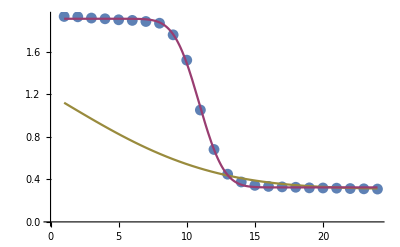

```mathematica
f[x_]:=a Erf[b( x-c)]+d;

a0=If[First@l<Last@l,1,-1] (Max@l-Min@l)/2
b0=2/Length@l;
c0=1;
d0=(Max@l+Min@l)/2;

fit=FindFit[l,f[x],{{a,a0},{b,b0},{c,c0},{d,d0}},x]

(*{a->-18.4315,b->0.0721048,c->4.33237,d->17.823}*)

Show[ListPlot[l],Plot[f[x]/.{a->a0,b->b0,c->c0,d->d0},{x,1,Length@l},PlotStyle->ColorData[1][3]],Plot[f[x]/.fit,{x,1,Length@l},PlotStyle->ColorData[1][2]]]
```

```mathematica
Solve[D[D[a Erf[b( x-c)]+d,x],x]==0,x]
```

{{x→c}}